# Radial Offset

## streakline.c

version 8 -  initial positions of ejected stars 
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU 
radial offsets = 0.2,0.2

```mathematica
c8cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",6001,1;;2}];
c8dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,1;;2}];
c8lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,3;;4}];
c8ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,5;;6}];
c8tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,7;;8}];
c8ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,9;;10}];
```

Import::noelem: The Import element "6001" is not present when importing as CSV.

## streakline.chpl

version 21 - initial positions of stars at ejection (using c’s radial offsets)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU 
radial offsets = 0.2,0.2

```mathematica
ch21cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",6001,1;;2}];
ch21dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,1;;2}];
ch21lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,3;;4}];
ch21ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,5;;6}];
ch21tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,7;;8}];
ch21ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,9;;10}];
```

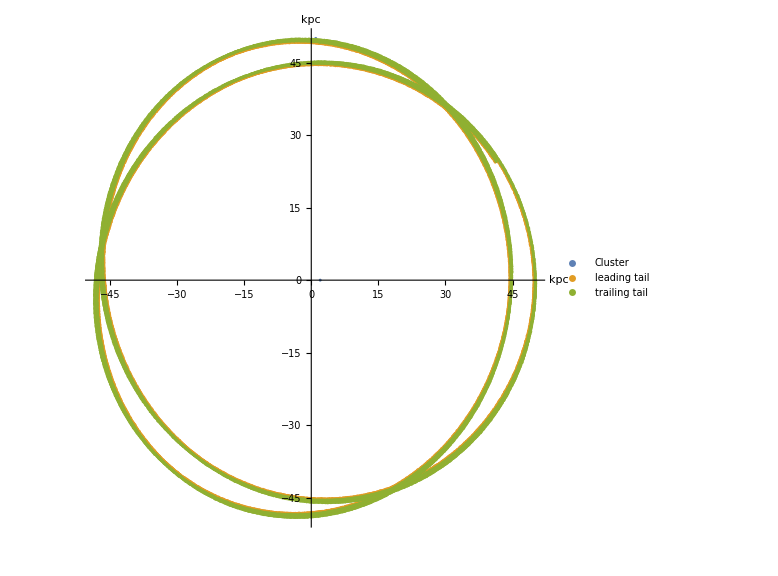

```mathematica
ch21graph = ListPlot[{ch21cl,ch21lt,ch21tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 22 - initial positions of stars at ejection (using chapel’s random numbers)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU 
radial offsets = 0.2, 0.2

```mathematica
ch22cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",6001,1;;2}];
ch22dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,1;;2}];
ch22lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,3;;4}];
ch22ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,5;;6}];
ch22tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,7;;8}];
ch22ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,9;;10}];
```

## Differences

c version 8 vs chapel version 21

```mathematica
diffc8ch21cl = Differences[{c8cl,ch21cl}]
diffc8ch21dt = Differences[{c8dt,ch21dt}]
diffc8ch21lt = Differences[{c8lt,ch21lt}]
diffc8ch21ltv = Differences[{c8ltv,ch21ltv}]
diffc8ch21tt = Differences[{c8tt,ch21tt}]
diffc8ch21ttv = Differences[{c8ttv,ch21ttv}]
```

{{50.0086-$Failed,-1.61672×10^-12-$Failed}}

{{{-41.2156,-24.381},{-41.0902,-24.4947},{-40.9451,-24.716},{-40.911,-24.9165},5991,{-49.8834,0.618205},{-49.7808,0.498806},{-49.8148,0.32144},{-49.8058,0.134146}}}
 |  |  |  |

{{{41.1314,24.4007-0.0000000.058310},{41.0071,24.6003-0.0000000.072821},{40.921,24.7564-0.0000000.106393},5993,{49.8679,-0.442347-0.0000000.226254},{49.883,-0.18501-0.0000000.193350},{49.8775,0.00113898-0.0000000.202750}}}
 |  |  |  |

{{{-0.116762,-41.1314},{-0.158192,-41.0071},{-0.0915411,-40.921},5993,{-0.134242,-49.8679},{-0.139157,-49.883},{-0.134146,-49.8775}}}
 |  |  |  |

{{{16.9558,24.534},{16.6553,24.7225},{16.4455,24.8658},{16.1176,25.0436},5991,{50.7407,-0.590169},{50.6051,-0.346334},{50.3629,-0.14039},{50.1547,-0.0193649}}}
 |  |  |  |

{{{-2.64701×10^-7,-41.3565},{-2.65202×10^-7,-41.2556},{-2.66152×10^-7,-41.2019},{-2.66014×10^-7,-41.0459},5992,{-1.80212×10^-7,-50.1628},{-1.80946×10^-7,-50.1779},{-1.81729×10^-7,-50.1558}}}
 |  |  |  |

c version 8 vs chapel version 22

```mathematica
diffc8ch22cl = Differences[{c8cl,ch22cl}]
diffc8ch22dt = Differences[{c8dt,ch22dt}]
diffc8ch22lt = Differences[{c8lt,ch22lt}]
diffc8ch22ltv = Differences[{c8ltv,ch22ltv}]
diffc8ch22tt = Differences[{c8tt,ch22tt}]
diffc8ch22ttv = Differences[{c8ttv,ch22ttv}]
```

{{50.0086-$Failed,-1.61672×10^-12-$Failed}}

{{{-41.1916,-24.4508},{-40.9738,-24.5012},{-40.9699,-24.7318},{-40.8179,-24.8799},{-40.7848,-25.0659},{-40.5315,-25.2005},{-40.385,-25.2327},{-40.371,-25.3625},{-40.245,-25.5799},{-40.1534,-25.737},5979,{-49.9322,1.72987},{-49.8806,1.59363},{-49.8534,1.39135},{-49.8728,1.25044},{-49.7543,1.00642},{-49.9624,0.917715},{-49.8529,0.597419},{-49.8242,0.482351},{-49.8747,0.271443},{-49.9319,0.150129}}}
 |  |  |  |

{{{41.1422,24.4155-0.0000000.058310},{41.0882,24.5686-0.0000000.072821},{40.9087,24.7474-0.0000000.106393},{40.8421,24.8527-0.0000000.028381},{40.6706,25.0794-0.0000000.149844},{40.595,25.1717-0.0000000.089320},{40.4229,25.3348-0.0000000.117844},{40.344,25.4724-0.0000000.062079},5984,{49.8362,-1.11898-0.0000000.088121},{49.8353,-0.903049-0.0000000.125910},{49.8331,-0.675254-0.0000000.108644},{49.8614,-0.56639-0.0000000.121762},{49.8424,-0.356725-0.0000000.226254},{49.8525,-0.173014-0.0000000.193350},{49.8462,-0.0152203-0.0000000.202750}}}
 |  |  |  |

{{{-0.116762,-41.1314},{-0.158192,-41.0071},{-0.0915411,-40.921},{-0.0452931,-40.8305},{-0.113223,-40.6953},{-0.0593921,-40.5741},{-0.111315,-40.456},{-0.0787691,-40.4311},5984,{-0.107864,-49.8545},{-0.150109,-49.8521},{-0.147768,-49.8541},{-0.071366,-49.8753},{-0.134242,-49.8679},{-0.139157,-49.883},{-0.134146,-49.8775}}}
 |  |  |  |

{{{17.0125,24.5581},{16.6934,24.7706},{16.4242,24.8917},{16.1793,25.09},{15.8218,25.1179},{15.6078,25.4044},{15.3782,25.4974},{15.0695,25.6288},{14.8836,25.7951},5981,{51.5347,-1.46841},{51.391,-1.33391},{51.2204,-1.09786},{51.1159,-0.892977},{50.8696,-0.703544},{50.7188,-0.538229},{50.6028,-0.364863},{50.3228,-0.217324},{50.1742,-0.0229213}}}
 |  |  |  |

{{{-2.64991×10^-7,-41.3565},{-2.6523×10^-7,-41.2556},{-2.66218×10^-7,-41.2019},{-2.65863×10^-7,-41.0459},{-2.66665×10^-7,-40.9697},{-2.66255×10^-7,-40.8184},{-2.66425×10^-7,-40.7531},{-2.66998×10^-7,-40.6638},5983,{-1.76512×10^-7,-50.1628},{-1.7707×10^-7,-50.1338},{-1.78127×10^-7,-50.1416},{-1.78432×10^-7,-50.1875},{-1.79859×10^-7,-50.1732},{-1.80292×10^-7,-50.1628},{-1.81189×10^-7,-50.1779},{-1.81651×10^-7,-50.1558}}}
 |  |  |  |

## chapel random function

testing random stream’s distribution. Creates an even distribution of numbers between 0 and 1.

Analyzing chapel random stream of 10,000 random numbers

```mathematica
randnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran.csv",{"Data",1;;10000,1}];
randmean = Mean[randnum]
randnumsd = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 10,000 numbers

```mathematica
randnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran1.csv",{"Data",1;;10000,1}];
randmean1 = Mean[randnum]
randnumsd1 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 5000 numbers

```mathematica
randnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran2.csv",{"Data",1;;5000,1}];
randmean2 = Mean[randnum]
randnumsd2 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 1000 numbers

```mathematica
randnum3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran3.csv",{"Data",1;;1000,1}];
randmean3 = Mean[randnum]
randnumsd3 = StandardDeviation[randnum]
```

0.500356

0.288492

## C random function

```mathematica
crandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest7.csv", {"Data",1,1;;6000}];
crandmean = Mean[crandnum]
crandnumsd = StandardDeviation[crandnum]
```

0.0112011

1.00299

## New Chapel Random function

for 10,000 numbers

```mathematica
nrandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran.csv",{"Data",1;;10000,1}];
nrandmean = Mean[nrandnum]
nrandnumsd = StandardDeviation[nrandnum]
```

0.00497026

1.00496

```mathematica
nrandnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran1.csv",{"Data",1;;10000,1}];
nrandmean = Mean[nrandnum1]
nrandnumsd = StandardDeviation[nrandnum1]
```

0.00418006

0.995367

```mathematica
nrandnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran2.csv",{"Data",1;;10000,1}];
nrandmean = Mean[nrandnum2]
nrandnumsd = StandardDeviation[nrandnum2]
```

-0.0190909

0.992605